```mathematica
4*0.067
```

0.268

```mathematica
Vddπ = 1.0; Vddσ = -1.5; Vddδ = -0.25;  θ=-(45Pi/180)+(11Pi/180);  
2/3(Vddπ+Vddδ+Vddπ Cos[2 θ]^2+Vddσ Sin[2θ]^2)
4/3((Vddπ+Vddδ) Cos[2θ]+Vddσ Cos[2θ]^2-Vddπ Sin[2θ]^2)
4/3 (Vddπ+Vddδ) Cos[2θ]
```

-0.266117

-1.05228

0.374607

```mathematica
4/3((Vddπ+Vddδ) Cos[2θ]+Vddσ Cos[2θ]^2-Vddπ Sin[2θ]^2)
```

1.33333

-1.

```mathematica
Vddπ =1.0; Vddσ = -1.5; Vddδ = -0.25;  θ=(11Pi/180)+-π/4;  
4/3((Vddπ+Vddδ) Cos[2θ]+Vddσ Cos[2θ]^2-Vddπ Sin[2θ]^2)
```

-1.05228

```mathematica
Vddπ =1.0; Vddσ = -1.5; Vddδ =-0.25;  θ=(11Pi/180);  
2/3(Vddπ+Vddδ+Vddπ Sin[2 θ]^2+Vddσ Cos[2θ]^2)
2/3((Vddπ+Vddδ) Cos[2θ]-Vddσ Sin[2θ]^2+Vddπ Cos[2θ]^2)
Vddπn = 0.07; Vddσn = -1.5*0.07; Vddδn = -0.25*0.07;  θ=(11Pi/180);  
2/3(Vddπn+Vddδn+Vddπn Cos[2 θ]^2+Vddσn Sin[2θ]^2)
```

-0.266117

1.17704

0.0652948

```mathematica
Clear[Vddπ,Vddδ,θ];
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

-Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

-Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

```mathematica
(**)
```

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

```mathematica
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

-Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

-Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

```mathematica
Clear[Vddπ,Vddδ,θ,Vddσ];
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->0}//FullSimplify
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π/2}//FullSimplify
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π}//FullSimplify
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->3π/2}//FullSimplify
```

Vddπ Cos[2 θ]^2+Vddσ Sin[2 θ]^2

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

```mathematica
(**)
```

Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

```mathematica
Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2-(1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ]))//Simplify
```

0

```mathematica
Cos[2(-π/4+a)]//FullSimplify
```

Sin[2 a]

```mathematica
Solve[2/3(x+Vddδ*x+Vddπ*x Cos[2 θ]^2+Vddσ*x Sin[2θ]^2)==0.066,x]
```

{{x→0.070756}}

```mathematica
Integrate[(Exp[-x/(2*4)] x/4)(Exp[(-(x-2))/(2*4)](x-2)/4),{x,0, Infinity}]//N
Integrate[(Exp[-x/(2*4)] x/4)(Exp[(-(x-4))/(2*4)](x-4)/4),{x,0, Infinity}]//N
```

7.70415

6.59489

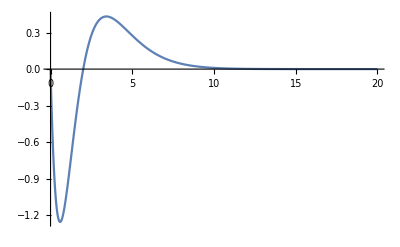

```mathematica
Plot[(Exp[-x/2]x)(Exp[(-(x-2))/2](x-2)),{x,0,20},PlotRange->All]
```